```mathematica
AppendTo[$Path, FileNameJoin[{$HomeDirectory,"network-similarity"}]];
```

```mathematica
g = Import["citation_network.gml", ImageSize->Full];
```

(collapsed) Timing for our citation network and the Zewail and SciMet datasets.

```mathematica
Timing[Import["citation_network.gml"];]
```

{119.234,Null}

```mathematica
Timing[Import["sciMet_dataset.gml",ImageSize->Full];]
Timing[Import["zewail_dataset.gml"];]
```

{2.73438,Null}

{2.98438,Null}

```mathematica
gU = UndirectedGraph[g, Options[g]];
gCC = Subgraph[g,WeaklyConnectedComponents[g][[1]]];
```

(collapsed) Making the degMimic graph variants and their pruned versions

```mathematica
outStubs=VertexOutDegree[g];
inStubs = VertexInDegree[g];
vertexlist=Range[VertexCount[g]];
edgelist={};
For[i=1,i≤EdgeCount[g],i++,
source = RandomSample[outStubs->vertexlist,1][[1]];
target = RandomSample[inStubs->vertexlist,1][[1]];
outStubs[[source]]-=1;
inStubs[[target]]-=1;
AppendTo[edgelist,source->target];]
degMimic=Graph[vertexlist,edgelist,ImageSize->Full];
degMimicU = UndirectedGraph[degMimic];
degMimicCC = Subgraph[degMimic,WeaklyConnectedComponents[degMimic][[1]]];
parentsDegMimic = Position[VertexOutDegree[degMimic], _?(#>0&)] // Flatten;
popularDegMimic = Position[VertexInDegree[degMimic], _?(#>1&)] // Flatten;
prunedDegMimic= Subgraph[degMimic, Union[parents, popular],Options[degMimic],VertexSize->Large];
prunedDegMimicU = UndirectedGraph[prunedDegMimic, Options[prunedDegMimic]];
prunedDegMimicCC =Subgraph[prunedDegMimic,WeaklyConnectedComponents[prunedDegMimic][[1]],Options[prunedDegMimic],ImageSize->Full];
```

Union::normal: Nonatomic expression expected at position 1 in parents∪popular.

Part::partw: Part 1 of {} does not exist.

(collapsed) Making the sciMet, zewail, and random graph variants

```mathematica
sciMet = Import["sciMet_dataset.gml"];
sciMetU = UndirectedGraph[sciMet ];
sciMetCC = Subgraph[sciMet ,WeaklyConnectedComponents[sciMet ][[1]]];

zewail= Import["zewail_dataset.gml"];
zewailU = UndirectedGraph[zewail];
zewailCC = Subgraph[zewail,WeaklyConnectedComponents[zewail][[1]]];

random = RandomGraph[{VertexCount[g],EdgeCount[g]},DirectedEdges->True];
randomU = UndirectedGraph[random ];
randomCC = Subgraph[random ,WeaklyConnectedComponents[random ][[1]]];
```

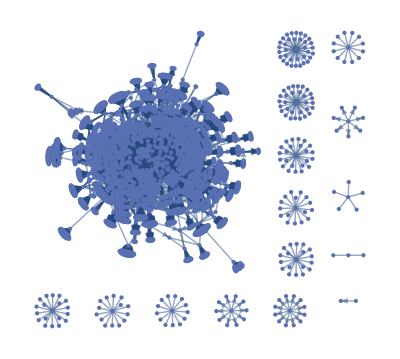

```mathematica
Show[g,ImageSize->Full]
```

```mathematica
GraphicsGrid[{{sciMet, zewail}},ImageSize->Full]
Show[sciMet,ImageSize->Full]
Show[zewail,ImageSize->Full]
```

-Graphics-

-Graphics-

-Graphics-

(collapsed) Definition of printStats[g] : Prints vertex count, edge count, mean degree, diameter, number of components, fraction of vertices with children, fraction in giant component, assortativity by indegree, assortativity by outdegree

```mathematica
printStats[degMimic_]:=
Print[VertexCount[degMimic],"\n",EdgeCount[degMimic],"\n",
EdgeCount[degMimic]/VertexCount[degMimic]//N,"\n",
GraphDiameter[UndirectedGraph[Subgraph[degMimic,WeaklyConnectedComponents[degMimic][[1]]]]],"\n",
Length[WeaklyConnectedComponents[degMimic]],"\n",
Length[Position[VertexOutDegree[degMimic], _?(#>0&)] // Flatten]/
VertexCount[degMimic]//N,"\n",
Length[VertexList[Subgraph[degMimic,WeaklyConnectedComponents[degMimic][[1]]]]]/Length[VertexList[degMimic]]//N,"\n",
GraphAssortativity[ReverseGraph[degMimic]]//N,"\n",
GraphAssortativity[degMimic]//N]
```

```mathematica
printStats[degMimic]
printStats[prunedDegMimic]
```

5793
7491
1.29311
9
3
0.0379769
0.999137
-0.00843757
-0.00696091

1077
2775
2.5766
7
3
0.201486
0.998143
-0.00732582
-0.0132293

```mathematica
parents = Position[VertexOutDegree[g], _?(#>0&)] // Flatten;
popular = Position[VertexInDegree[g], _?(#>1&)] // Flatten;
pruned= Subgraph[g, Union[parents, popular],Options[g],VertexSize->Large];
prunedU = UndirectedGraph[pruned, Options[pruned]];
prunedCC =Subgraph[pruned,WeaklyConnectedComponents[pruned][[1]],Options[pruned],ImageSize->Full];
```

```mathematica
partition = FindGraphPartition[pruned,2];
gA = Subgraph[pruned, partition[[1]], Options[pruned],VertexSize->Large,ImageSize->Full];
gB = Subgraph[pruned, partition[[2]], Options[pruned],VertexSize->Large];
```

(collapsed) Cell for making the table (outdated)

```mathematica
Export[FileNameJoin[{$HomeDirectory,"network-similarity/full_table_raw.txt"}],{{"","Full network (G)","Pruned network (P)","SciMet","Zewail","Random network of same size as G","Random network with same degree sequence as G"},{"Vertices",VertexCount[g],VertexCount[prunedCC],VertexCount[sciMet],VertexCount[zewail],VertexCount[random],VertexCount[degMimic]},{"Edges",EdgeCount[g],EdgeCount[prunedCC],EdgeCount[sciMet],EdgeCount[zewail],EdgeCount[random],EdgeCount[degMimic]},{"Diameter",GraphDiameter[UndirectedGraph[gCC]],GraphDiameter[UndirectedGraph[prunedCC]],GraphDiameter[UndirectedGraph[sciMetCC]],GraphDiameter[UndirectedGraph[zewailCC]],GraphDiameter[UndirectedGraph[randomCC]],GraphDiameter[UndirectedGraph[degMimicCC]]},{"Connected components",Length[WeaklyConnectedComponents[g]],Length[WeaklyConnectedComponents[prunedCC]],Length[WeaklyConnectedComponents[sciMet]],Length[WeaklyConnectedComponents[zewail]],Length[WeaklyConnectedComponents[random]],Length[WeaklyConnectedComponents[degMimic]]},{"Fraction of vertices in giant component",Length[VertexList[gCC]]/Length[VertexList[g]]//N,Length[VertexList[prunedCC]]/Length[VertexList[prunedCC]]//N,Length[VertexList[sciMetCC]]/Length[VertexList[sciMet]]//N,Length[VertexList[zewailCC]]/Length[VertexList[zewail]]//N,Length[VertexList[randomCC]]/Length[VertexList[random]]//N,Length[VertexList[degMimicCC]]/Length[VertexList[degMimic]]//N},{"Assortativity by indegree",GraphAssortativity[ReverseGraph[g]]//N,GraphAssortativity[ReverseGraph[prunedCC]]//N,GraphAssortativity[ReverseGraph[sciMet]]//N,GraphAssortativity[ReverseGraph[zewail]]//N,GraphAssortativity[ReverseGraph[random]]//N,GraphAssortativity[ReverseGraph[degMimic]]//N},{"Assortativity by outdegree",GraphAssortativity[g]//N,GraphAssortativity[prunedCC]//N,GraphAssortativity[sciMet]//N,GraphAssortativity[zewail]//N,GraphAssortativity[random]//N,GraphAssortativity[degMimic]//N},{"Assortativity by year",GraphAssortativity[g,"year"]//N},{"Assortativity by reference count",GraphAssortativity[g,"referenceCount"]//N},{"Assortativity by citation count",GraphAssortativity[g,"citationCount"]//N}}]
```

C:\Users\Marissa\network-similarity\full_table_raw.txt

(collapsed) Indegree and outdegree histograms (just full and pruned)

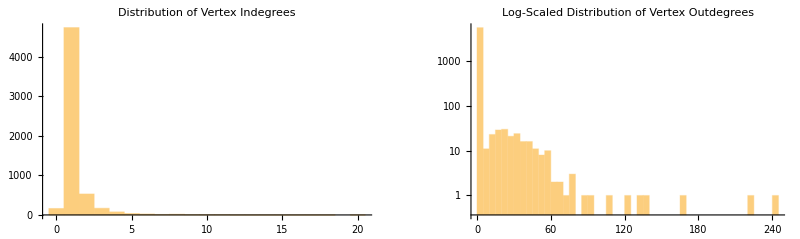

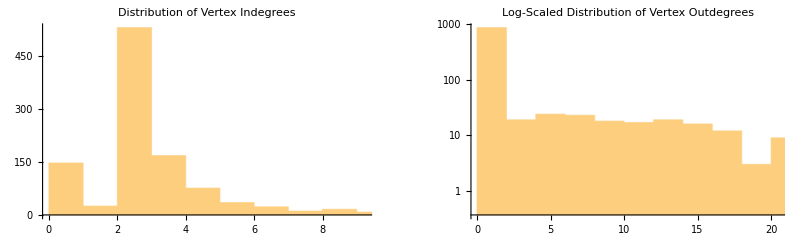

```mathematica
GraphicsGrid[{{Histogram[VertexInDegree[g],PlotLabel->Style["Distribution of Vertex Indegrees",Black,FontFamily->"Helvetica"]],Histogram[VertexOutDegree[g],50,ScalingFunctions->"Log", PlotLabel->Style["Log-Scaled Distribution of Vertex Outdegrees",Black,FontFamily->"Helvetica"]]}},Frame->None,ImageSize->Full]
GraphicsGrid[{{Histogram[VertexInDegree[g1CC],PlotLabel->Style["Distribution of Vertex Indegrees",Black,FontFamily->"Helvetica"]],Histogram[VertexOutDegree[g1CC],50,ScalingFunctions->"Log", PlotLabel->Style["Log-Scaled Distribution of Vertex Outdegrees",Black,FontFamily->"Helvetica"]]}},Frame->None,ImageSize->Full]
```

(collapsed) Histogram for citation counts

```mathematica
citationCounts = {};
For[i=1,i≤VertexCount[g],i++,
AppendTo[citationCounts, PropertyValue[{g,i},"citationCount"]]
]
GraphicsGrid[{{Histogram[citationCounts,PlotLabel->Style["Distribution of Citation Counts",Black]]},
{Part[citationCounts, Ordering[citationCounts, All, Greater]][[;;50]]}}]
```

(collapsed) Statistics for partition modularity stuff

```mathematica
Print[GraphAssortativity[g,FindGraphPartition[g,2]]//N,"\t",
GraphAssortativity[g,FindGraphCommunities[g]]//N]
Print[GraphAssortativity[prunedCC,FindGraphPartition[prunedCC,2]]//N,"\t",
GraphAssortativity[prunedCC,FindGraphCommunities[prunedCC]]//N]
Print[GraphAssortativity[sciMet,FindGraphPartition[sciMet,2]]//N,"\t",
GraphAssortativity[sciMet,FindGraphCommunities[sciMetCC]]//N]
Print[GraphAssortativity[zewail,FindGraphPartition[zewail,2]]//N,"\t",
GraphAssortativity[zewail,FindGraphCommunities[zewail]]//N]
Print[GraphAssortativity[random,FindGraphPartition[random,2]]//N,"\t",
GraphAssortativity[random,FindGraphCommunities[random]]//N]
Print[GraphAssortativity[degMimic,FindGraphPartition[degMimic,2]]//N,"\t",
GraphAssortativity[degMimic,FindGraphCommunities[degMimic]]//N]
```

0.790707	0.907459

0.85803	0.736534

0.868984	0.78031

0.919215	0.878669

0.817111	0.733637

0.802708	0.791902

```mathematica
modgraphs = {gParents, g, prunedCC, sciMet, zewail, random, degMimic};
For[i=1,i≤7,i++,
wrongside =0;
gpartition = FindGraphPartition[modgraphs[[i]]];
gcommunities=FindGraphCommunities[modgraphs[[i]]];
For[j=1,j≤Length[gcommunities],j++,
sideA =Length[Intersection[gpartition[[1]],gcommunities[[j]]]];
sideB =Length[Intersection[gpartition[[2]],gcommunities[[j]]]];
If[sideA≥sideB,wrongside+=sideB];
If[sideA<sideB,wrongside+=sideA];
];
Print[wrongside,", ",  VertexCount[modgraphs[[i]]],", ", wrongside/VertexCount[modgraphs[[i]]]//N];
]
```

Intersection::normal: Nonatomic expression expected at position 1 in gParents∩gParents.

Part::partw: Part 2 of FindGraphPartition[gParents] does not exist.

Intersection::normal: Nonatomic expression expected at position 2 in FindGraphPartition[gParents]⟦2⟧∩gParents.

2, VertexCount[gParents], 2./VertexCount[gParents]

597, 5793, 0.103055

120, 1062, 0.112994

0, 1094, 0.

0, 3147, 0.

1870, 5793, 0.322803

1876, 5793, 0.323839

```mathematica
graphs = {prunedCC, gA, gB};
graphnames = {"'pruned'","'gA'","'gB'"};
```

(collapsed) Display top values for indegree, outdegree, and betweenness for networks in ‘graphs’

```mathematica
For[i=1,i≤3,i++,
tops = Part[VertexList[graphs[[i]]], Ordering[DegreeCentrality[graphs[[i]],"In"], All, Greater]];
For[j=1,j≤10,j++,Print[tops[[j]],":{'", PropertyValue[{graphs[[i]],tops[[j]]},"title"],"', ",graphnames[[i]],", 'indegree', ",VertexInDegree[graphs[[i]],tops[[j]]],"},"];];
]
```

```mathematica
For[i=1,i≤3,i++,
tops = Part[VertexList[graphs[[i]]], Ordering[DegreeCentrality[graphs[[i]],"Out"], All, Greater]];
For[j=1,j≤10,j++,Print[tops[[j]],":{'", PropertyValue[{graphs[[i]],tops[[j]]},"title"],"', ",graphnames[[i]],", 'outdegree', ",VertexOutDegree[graphs[[i]],tops[[j]]],"},"];];
]
```

```mathematica
For[i=1,i≤3,i++,
b = BetweennessCentrality[UndirectedGraph[graphs[[i]]]];
tops = Part[VertexList[graphs[[i]]], Ordering[b, All, Greater]];
For[j=1,j≤10,j++,Print[tops[[j]],":{'", PropertyValue[{graphs[[i]],tops[[j]]},"title"],"', ",graphnames[[i]],", 'betweenness', ",j,"},"];];
Print["\n\n"];
]
```

(collapsed) Displayed highest closeness centrality verts and realized that I should do it undirected

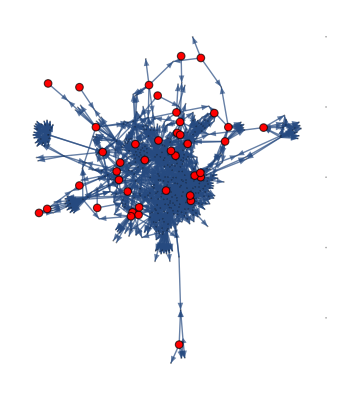

```mathematica
verts = VertexList[gA];
For[i=1,i≤VertexCount[gA],i++,
If[ClosenessCentrality[gA][[i]]==1.0,PropertyValue[{gA,verts[[i]]},VertexStyle]=Red;
PropertyValue[{gA,verts[[i]]},VertexSize]=10]
]
Show[gA]
```

(collapsed) Display top values for closeness and HITS hub/authority, for networks in ‘graphs’

```mathematica
For[i=1,i≤3,i++,
b = ClosenessCentrality[UndirectedGraph[graphs[[i]]]];
tops = Part[VertexList[graphs[[i]]], Ordering[b, All, Greater]];
For[j=1,j≤12,j++,Print[tops[[j]],":{'", PropertyValue[{graphs[[i]],tops[[j]]},"title"],"', ",graphnames[[i]],", 'closeness', ",j,"},"];];
Print["\n\n"];
]
```

```mathematica
For[i=1,i≤3,i++,
Print["****",graphnames[[i]],"****"];
Print["Authorities"];
b =HITSCentrality[graphs[[i]]][[1]];
tops = Part[VertexList[graphs[[i]]], Ordering[b, All, Greater]];
For[j=1,j≤12,j++,Print[tops[[j]],": ", PropertyValue[{graphs[[i]],tops[[j]]},"title"],", ",j];];
Print["Hubs"];
b = HITSCentrality[graphs[[i]]][[2]];
tops = Part[VertexList[graphs[[i]]], Ordering[b, All, Greater]];
For[j=1,j≤12,j++,Print[tops[[j]],": ", PropertyValue[{graphs[[i]],tops[[j]]},"title"],", ",j];];
Print["\n"]]
```

```mathematica
For[i=1,i≤3,i++,
Print["****",graphnames[[i]],"****"];
Print["Authorities"];
b =HITSCentrality[graphs[[i]]][[1]];
tops = Part[VertexList[graphs[[i]]], Ordering[b, All, Greater]];
For[j=1,j≤10,j++,Print[tops[[j]],": ", PropertyValue[{graphs[[i]],tops[[j]]},"title"],", ",j];];
Print["Hubs"];
b = HITSCentrality[graphs[[i]]][[2]];
tops = Part[VertexList[graphs[[i]]], Ordering[b, All, Greater]];
For[j=1,j≤10,j++,Print[tops[[j]],": ", PropertyValue[{graphs[[i]],tops[[j]]},"title"],", ",j];];
Print["\n"]]
```

(collapsed) Create parent network and display it and its most cited nodes

```mathematica
outdegrees = VertexOutDegree[g];
parents = Position[outdegrees, _?(#>0&)] // Flatten;
gParents = Subgraph[g,parents, Options[g], ImageSize->Full];
```

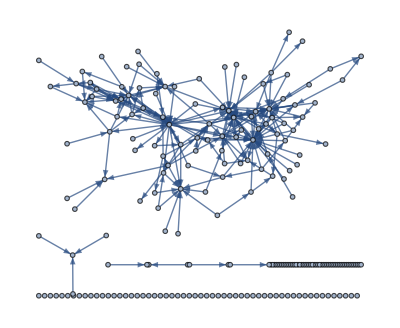

{{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.},{162,25,10,6,2,2,3,1,2,2,1,1,0,0,0,1,0,0,0,0,2}}

Title | Indegree | Citation Count
THIRTY YEARS OF GRAPH MATCHING IN PATTERN RECOGNITION | 20 | 467.
An Algorithm for Subgraph Isomorphism | 20 | 762.
An eigendecomposition approach to weighted graph matching problems | 15 | 321.
On Graph Kernels: Hardness Results and Efficient Alternatives | 11 | 111.
Error correcting graph matching: on the influence of the underlying cost function | 10 | 118.
A new graph-based method for pairwise global network alignment | 9 | 76.
Modeling cellular machinery through biological network comparison | 9 | 271.
Local graph alignment and motif search in biological networks | 8 | 86.
A linear programming approach for the weighted graph matching problem | 8 | 113.
IsoRankN: spectral methods for global alignment of multiple protein networks | 7 | 141.

```mathematica
Show[gParents]
indegrees = VertexInDegree[gParents];
posIn = Position[indegrees, _?(#>0&)];
mostCited = Part[VertexList[gParents], Ordering[DegreeCentrality[gParents,"In"], All, Greater]];

HistogramList[indegrees]
popularParents = {{"Title","Indegree","Citation Count"}};
For[i=1,i≤10,i++,
AppendTo[popularParents,{PropertyValue[{gParents,mostCited[[i]]},"title"], VertexInDegree[gParents,mostCited[[i]]], PropertyValue[{gParents, mostCited[[i]]},"citationCount"]}]
]
Grid[popularParents,
Spacings->{1,1},Alignment->Left,Frame->All, ItemStyle->{"Text",FontFamily->"Helvetica"}]
```

For a given node, print the following with respect to the full graph, pruned graph, gA, and gB (whichever it’s in): indegree, outdegree, (betweenness rank, closeness rank, authority rank, hub rank)

```mathematica
vertices = {1,3,97,26,29,39,43,49,53,66,71,74,80,82,59,90,98,103,114,115,5,123,135,193,268,320,348,350,352,353,356,357,360,564,770,772,842,868,874,1198,1310,1316,1419,2015,2140,2432,2577,2593,2631,3025,3158,3175,3230,3398,4094,4217,4655,4679,4962,5345};
vertices =Sort[vertices];
```

```mathematica
For[i=1,i≤Length[vertices],i++,
vert = VertexList[g][[vertices[[i]]]];
Print[vert,", ", PropertyValue[{g,vert},"title"]];
]
```

```mathematica
parents = Position[VertexOutDegree[g], _?(#>0&)] // Flatten;
popular = Position[VertexInDegree[g], _?(#>1&)] // Flatten;
pruned= Subgraph[g, Union[parents, popular],Options[g],VertexSize->Large];
```

```mathematica
prunedCC =Subgraph[pruned,WeaklyConnectedComponents[pruned][[1]],Options[pruned],ImageSize->Full];
```

```mathematica
partition = FindGraphPartition[prunedCC,2];
gA = Subgraph[prunedCC, partition[[1]], Options[pruned],VertexSize->Large,ImageSize->Full];
gB = Subgraph[prunedCC, partition[[2]], Options[pruned],VertexSize->Large];
```

```mathematica
If[MemberQ[VertexList[gB],vert],Print["In group 2"]];
```

```mathematica
inouts = {{"ID", "InDegree","OutDegree","Title"}};
For[i=1,i≤Length[vertices],i++,
vert = vertices[[i]];
If[MemberQ[VertexList[gB],vert],
AppendTo[inouts,{ vert,BetweennessCentrality[gB,vert],VertexOutDegree[gB,vert]}];]
]
Grid[inouts,Alignment->Left]
```

ID | InDegree | OutDegree | Title
1 | 4 | 56 | 
5 | 11 | 0 | 
26 | 6 | 26 | 
29 | 1 | 30 | 
49 | 2 | 22 | 
53 | 2 | 90 | 
59 | 11 | 0 | 
71 | 10 | 0 | 
74 | 8 | 12 | 
90 | 9 | 40 | 
97 | 12 | 0 | 
103 | 10 | 0 | 
114 | 5 | 35 | 
115 | 10 | 9 | 
770 | 12 | 0 | 
772 | 10 | 0 | 
868 | 11 | 0 | 
874 | 7 | 7 | 
1419 | 10 | 0 | 
2015 | 1 | 23 | 
3025 | 0 | 30 | 
3230 | 0 | 28 | 
4094 | 0 | 25 | 
4217 | 0 | 29 | 
4655 | 0 | 30 | 
4679 | 0 | 26 | 
5345 | 0 | 29 |

```mathematica
labels = Table[vertices[[i]]->Placed[Pane[PropertyValue[{g,vertices[[i]]},"title"],250,FrameMargins->None,ImageSize->Small,ImageSizeAction->"ShrinkToFit"],Center],{i,1,Length[vertices]}];
```

```mathematica
colorlabels = {};
For[i=1,i≤Length[vertices],i++,
If[MemberQ[VertexList[gA],vertices[[i]]],AppendTo[colorlabels,vertices[[i]]->Directive[LightGreen,EdgeForm[None]]]];
If[MemberQ[VertexList[gB],vertices[[i]]],AppendTo[colorlabels,vertices[[i]]->Directive[LightBlue,EdgeForm[None]]]];]
```

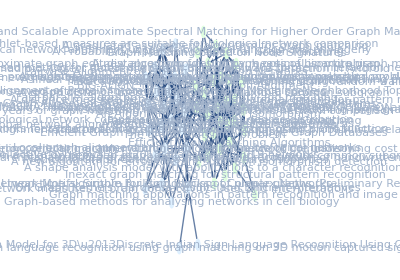

```mathematica
toRead =Graph[Subgraph[g, vertices, Options[g]],GraphLayout->{"SpringElectricalEmbedding","RepulsiveForcePower"->-2.5},VertexStyle->colorlabels,EdgeStyle->Arrowheads[Medium],VertexSize->{"Nearest",0.8},VertexLabels->Table[vertices[[i]]->Placed[Pane[Style[PropertyValue[{g,vertices[[i]]},"title"],LineSpacing->{1,0}],250,FrameMargins->None,ImageSize->Small,ImageSizeAction->"ShrinkToFit"],Center],{i,1,Length[vertices]}],AspectRatio->0.7, ImageSize->Full]
```

```mathematica
Length[AdjacencyList[g,vert]]
Length[Complement[AdjacencyList[g,vert],AdjacencyList[g,1],AdjacencyList[g,66]]]
```

```mathematica
VertexCount[gsub]
```

58

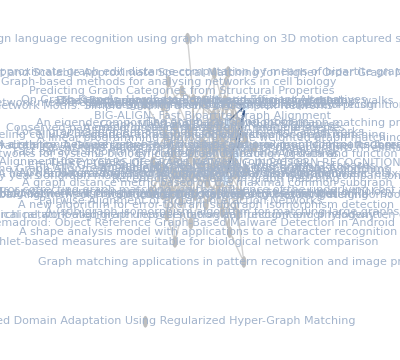

```mathematica
vert = 317;gsub = Subgraph[g,vertices,VertexLabels->labels,GraphLayout->{"SpringElectricalEmbedding","RepulsiveForcePower"->-2.5},EdgeStyle->Arrowheads[Medium],VertexStyle->EdgeForm[None],VertexSize->{"Nearest",0.8}];
HighlightGraph[toRead,NeighborhoodGraph[gsub,vert],GraphHighlightStyle->"DehighlightGray",VertexStyle->colorlabels,ImageSize->Full]
```